```mathematica
resultado=Import["majestad.mat","Table"]//ToExpression;
```

```mathematica
resultado//Dimensions
```

{40,12}

```mathematica
resultado[[1]]//Dimensions
```

{12}

```mathematica
Import["/home/david/libs/QuantumDavid.m"]
```

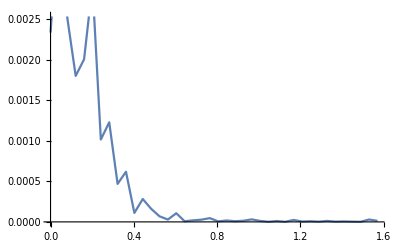

```mathematica
campo=linearmesh[0,Pi/2,40];
ListLinePlot[Table[{campo[[k]],resultado[[k]][[1]]},{k,1,40}]]
```

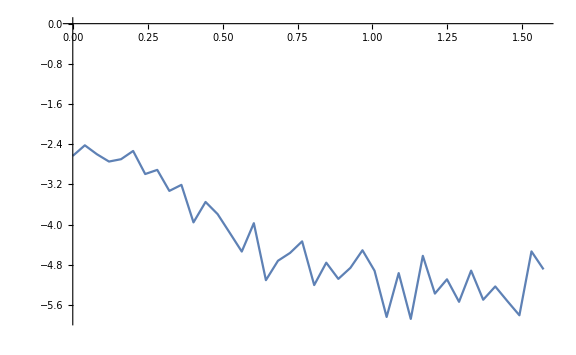
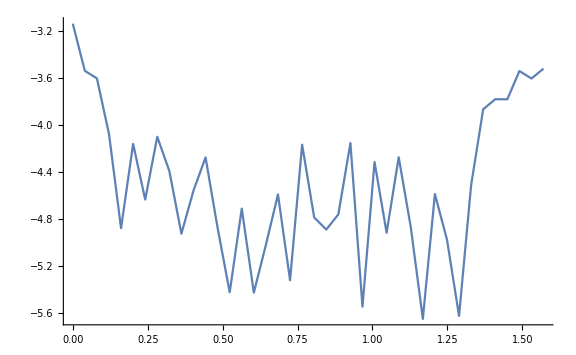
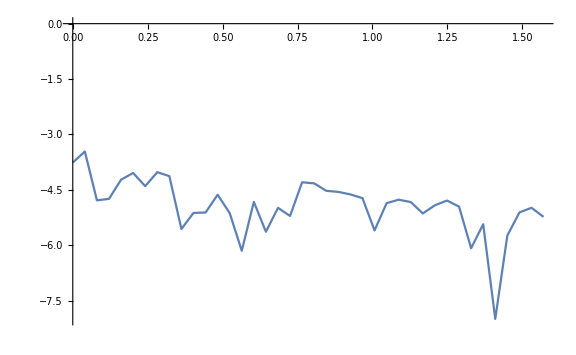
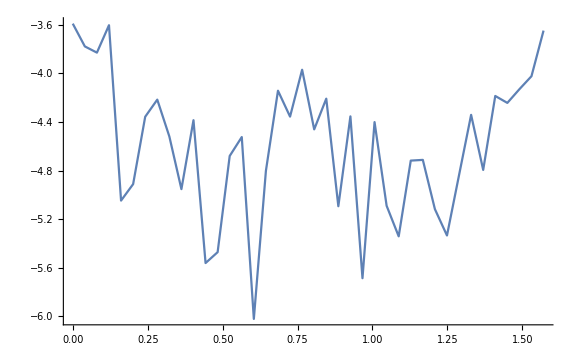
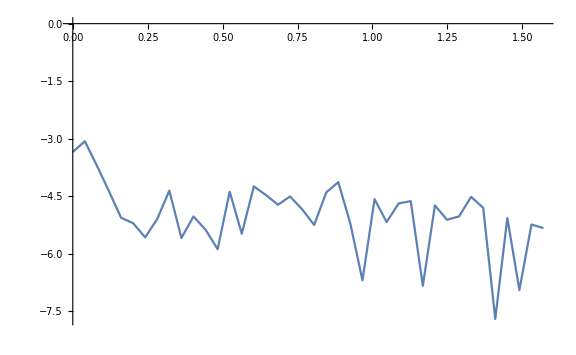
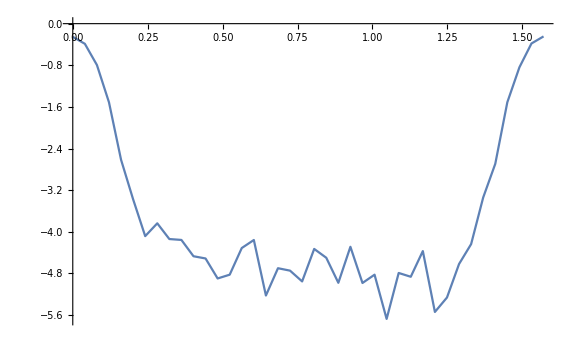
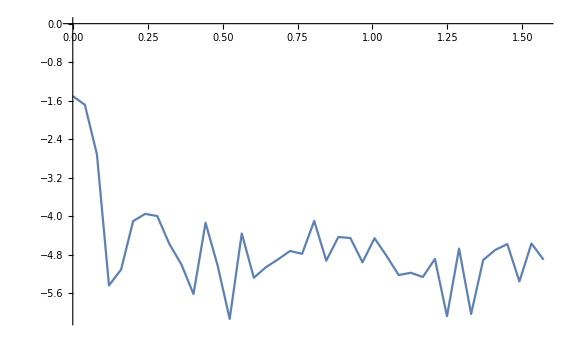
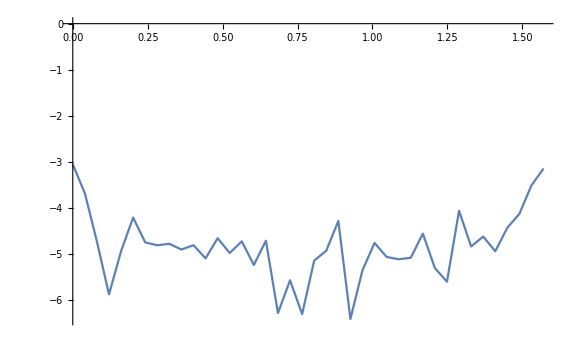

```mathematica
Table[ListLinePlot[Table[{campo[[k]],Log[10,resultado[[k]][[i]]]},{k,1,40}],ImageSize->Large],{i,1,12}]
```